```mathematica
SetDirectory["/Users/dluntzma/Desktop/DoubleSlit-ED"];
counts3 = Import["20141122_double_slit_bulb_counts3.csv"];
counts3;
```

```mathematica
θ = (x -x0 )/R;
α = π * a * Sin[θ]/λ;
β = π * d * Sin[θ]/λ; 

Subscript[i, 2] = i0 * (Sinc[α])^2 * Cos[β]^2;
```

```mathematica
x0= 6.4;
a = 0.09;
d = 0.383;
R = 550;
λ = .000546;
(*i0 = 300;*)
```

308.683 Cos[2203.72 Sin[1/550 (-6.4+x)]]^2 Sinc[517.845 Sin[1/550 (-6.4+x)]]^2

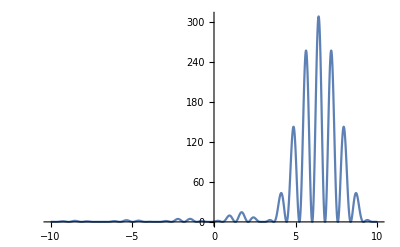

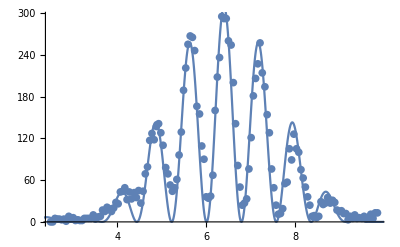

```mathematica
fit3 = NonlinearModelFit[counts3,Subscript[i, 2], i0, x];
Normal[fit3]
plot3 = Plot[fit3[x], {x, -10, 10}, PlotRange->All]
Show[ListPlot[counts3], plot3]
```

```mathematica
ChiSq3=∑_(j=1)^146 ((fit3["FitResiduals"][[j]])/(2(√counts3[[j,2]]-√1.68)))^2
RedChiSq3 = ChiSq3/7
```

855.847

122.264